# Cederberg Senior Scout Adventure 2014 Electronics Base Working

## Constants of the Thermistors

```mathematica
B = 3380;
Subscript[R, 0]=10000;
Subscript[T, 0]=273+25;
r=Subscript[R, 0] Exp[-B/Subscript[T, 0]] ;
```

## Equations of Thermistors

```mathematica
R[T_] = Subscript[R, 0] Exp[B(1/(273+T)-1/Subscript[T, 0])];
T[R_] := B/Log[R/r]-273;
```

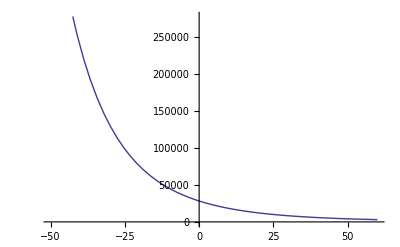

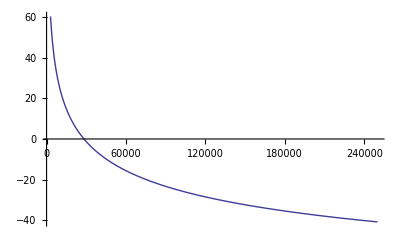

```mathematica
Plot[R[t],{t,-50,60}]
Plot[T[x],{x,3000,250000},PlotRange->All]
```

## Logarithm Approximation

```mathematica
Nodes ={20,40,60,100,200,300,500,1000,1500,2000,2500,3000,3500,4000,4500};
logValues = 100*Log[Nodes*1000];
hundlogthou[x_] = Interpolation[Thread[{Nodes,logValues}],x,InterpolationOrder->1];
```

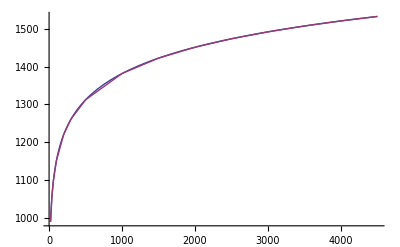

```mathematica
Plot[{100*Log[x*1000],hundlogthou[x]},{x,20,4500},PlotRange->All]
```

It can be shown that the propegation of error is proportional to the inverse square of the actual value

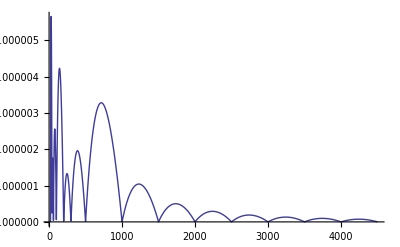

```mathematica
Plot[(100*Log[x*1000]-hundlogthou[x])/(100*Log[x*1000])^2,{x,20,4500},PlotRange->All]
```